```mathematica
SetDirectory["C:\\Users\\mi\\CLionProjects\\CDEv2\\cmake-build-debug"];
```

```mathematica
data = Import["data","Table"];
ls=ListLinePlot[#,PlotRange->{Full,{-1,1}}]&/@data;
anim=ListAnimate@ls
```

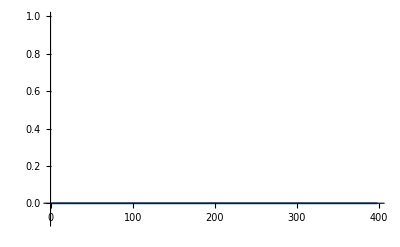

```mathematica
ListLinePlot[data[[23]],PlotRange->{Full,{-0.1,1}}]
```

```mathematica
Export["test2.gif",ls]
```

test2.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["test.gif"]]]
```

```mathematica
ListPlot3D[datas[[1]],PlotRange->{Full,Full,{-0.05,1}}]
```

```mathematica
Length@data
```

198